# Primer Examen Parcial

## MC-6003 II-2021 Teoría de Autómatas y Lenguajes Formales (13 Septiembre 2021)

Andrey Arguedas Espinoza - 2020426569

Oscar Rodríguez Arroyo - 2015183005

Oscar Salazar Lizano - 2020426732

## Instrucciones

El objetivo de este exámen no es el de evaluar la materia, sino más bien de ayudar a extender lo aprendido, y fortalecer el entendimiento general de la teoría de autómatas, y de su implementación.

El exámen se trabaja en grupos de 3/4 personas.

Recuerdo que la evaluación es un sistema de puntos, y ustedes pueden determinar si resuelven todas o solo algunas de las preguntas.

La entrega la hace solamente una persona del grupo (incluir el nombre de todos los miembros)

Se debe entregar este mimso Notebook con las respuestas

Tienen desde el Lunes 13 a las 8 de la mañana hasta el Sábado 18 a media noche para entregar el exámen.

Los puntos obtenidos son los mismos para cada miembro del grupo.

Si tiene preguntas, se hacen en el whatsapp de todo el grupo (no me envíe preguntas a modo personal)

Es permitido compartir y discutir entre grupos, pero cada respuesta de grupo es única, y se debe dar los créditos respectivos, en caso de que utilicen algún resultado parcial de otro grupo.

## Pregunta 1. (60 pts)

### Problema

a) Desarrolle una función en Mathematica FAtoRE[...], para poder obtener une expresión regular a partir de la definición de un automata finito en una asociación en Mathematica.  Puede utilizar cualquiera de los métodos vistos en clase.  En el desarrollo de la función, describa paso a paso como construye la función y justifique cada paso, de esa manera aunque no pueda crear la función, se le darán puntos parciales por cada parte. (45 pts)

b) muestre su funcionamiento con tres ejemplos, y compare e resultado de validación de un string del autómata, con su expresión regular equivalente. (15 pts)

### Respuesta

A continuación crearemos la función FAtoRE con el siguiente ejemplo :

```mathematica
ShowGraphDFA[δ_,states_List,q0_,q_List]:=Graph[
MapThread[DirectedEdge,{First/@Keys[δ],Values[δ]}],
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
EdgeWeight->Last/@Keys[δ],
EdgeLabels->"EdgeWeight",
VertexStyle->Join[{q0->White},Map[(#->Red)&,q]]
]
```

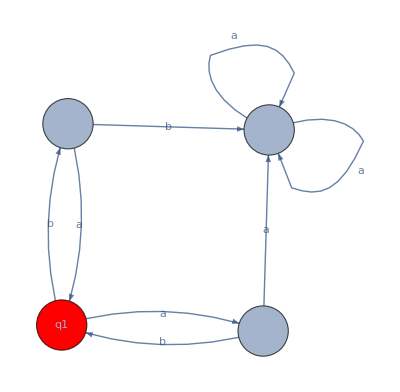

```mathematica
δ=Association[
{"q1","a"}->"q2",
{"q1","b"}->"q3",
{"q2","a"}->"q4",
{"q2","b"}->"q1",
{"q3","a"}->"q1",
{"q3","b"}->"q4",
{"q4","a"}->"q4",
{"q4","b"}->"q4"
];
ShowGraphDFA[δ,{"q1", "q2", "q3", "q4"},"q1",{"q1"}]
```

Para poder crear la función que convierte de un Automata Finito a Expression Regular usaremos el metido que hace uso del Teorema de Arden, el cual se puede definir como Q + RP = QP*.

Primero debemos obtener dada una asociación los estados y transiciones que entran hacia cada estado, por ejemplo para saber que estados y transiciones entran hacia el estado “q1”, lo podemos obtener de la siguiente manera :

```mathematica
Select[δ,#=="q1"&]
```

<|{q2,b}→q1,{q3,a}→q1|>

Como podemos observar obtenemos que al estado “q1” llegamos por medio de “q2 b” y de “q3 a”. Por lo que necesitamos una función encargada de darnos toda esta información de manera que q1 quede representado por la expresión “q1 =  q2 b +q3a”.

Definimos algunas variable para enviar por parámetros

```mathematica
FAstates = {"q1", "q2", "q3", "q4"};
finalState = "q1";
initialState = "q1";
expressionVars = {q1,q2,q3,q4};
statesSeparation = {"q1" -> " q1 ","q2" -> " q2 ","q3" -> " q3 ","q4" -> " q4 "};
nonFinalStates={"q1"};
```

Con getIncomingTransitions obtenemos una asociación de los estados y transiciones que entran a cada estado, por ejemplo con “q1” obtenemos {q2,b} → q1 y {q3,a} → q1.

```mathematica
getIncomingTransitions[δ_,states_] := Table[Select[δ,#==i&], {i,states}];
getIncomingTransitions[δ,FAstates]
```

{<|{q2,b}→q1,{q3,a}→q1|>,<|{q1,a}→q2|>,<|{q1,b}→q3|>,<|{q2,a}→q4,{q3,b}→q4,{q4,a}→q4,{q4,b}→q4|>}

Seguido de esto necesitamos construir las “formulas” o “expresiones” de una manera que siga el formato “q = q# a + q# b”. Para lograrlo aplicamos un StringRiffle sobre las llaves del resultado obtenido en getIncomingTransitions y en vez de “,” separamos con “+”

```mathematica
getExpresionValuesForStates[incomingTransitions_]:=Table[StringJoin[StringRiffle[Keys[i], " + "]],{i,incomingTransitions}];
```

```mathematica
getExpresionValuesForStates[getIncomingTransitions[δ,FAstates]]
```

{{q2, b} + {q3, a},{q1, a},{q1, b},{q2, a} + {q3, b} + {q4, a} + {q4, b}}

Como podemos observar  ahora tenemos una lista donde los elementos de cada expresión están separados por “+”, y para q1 podemos ver como la expresión se nos va formando en q1 =  {q2, b} + {q3, a}

Para poder crear las expresiones tal como las necesitamos definimos la función buildExpressions, esta se encarga de crear las expresiones tal como las necesitamos y ademas las metemos en una asociación, para que sea más fácil el accesarlos.

```mathematica
buildExpressions[states_, expressionValues_]:= Association[Table[states[[i]] -> StringReplace[expressionValues[[i]], {"{" -> "", "}" -> "", "," -> "", " " -> ""}],{i,Length[states]}]];
```

```mathematica
buildExpressions[FAstates, getExpresionValuesForStates[getIncomingTransitions[δ,FAstates]]]
```

<|q1→q2b+q3a,q2→q1a,q3→q1b,q4→q2a+q3b+q4a+q4b|>

Como podemos observar ahora tenemos una asociación  que dado un estado podemos obtener la expresión del mismo, ejemplo para q1 tenemos “q1 -> q2 b + q3 a”

Ahora debemos empezar a sustituir los estados que intervienen en el estado final para “despejar la ecuación”, esto hasta que ya no hayan mas estados por despejar que el mismo estado final, para esto definimos buildFinalStateExpression, la cual se encargará de darnos la expresión final ya con los estados despejados, por ejemplo en el caso de “q1” se va a despejar “q2” y “q3”.

```mathematica
buildFinalStateExpression[originalExpressions_, states_ , finalState_]:=StringReplace[originalExpressions[finalState],Table[i ->  originalExpressions[[i]],{i,states}]];
```

```mathematica
newExpression =buildFinalStateExpression[ buildExpressions[FAstates, getExpresionValuesForStates[getIncomingTransitions[δ,FAstates]]], FAstates, finalState]
```

q1ab+q1ba

Como podemos observar el estado está “pegado” a las variables del alfabeto por lo que debemos separarlas

```mathematica
separateStatesFromLanguage[expression_, rules_] := StringReplace[expression,  rules];
```

```mathematica
newExpression =separateStatesFromLanguage[newExpression, statesSeparation]
```

q1 ab+ q1 ba

Ahora podemos sacar el Factor Común

```mathematica
simplifyExpression[expression_, expressionVariables_] := ToString[Collect[ToExpression[expression],expressionVariables]];
```

```mathematica
newExpression =simplifyExpression[newExpression, expressionVars]
```

(ab + ba) q1

Finalmente aplicamos el teorema de Arden

```mathematica
generateArdensReplacementsRules[states_] := Union[Union[Table[StringJoin[i, " +"] -> "*",{i,states}], Table[StringJoin["+",i] -> "*",{i,states}]],Table[StringJoin[i] -> "*",{i,states}]] ;
```

```mathematica
ArdensRule[expression_, states_] :=StringReplace[expression, generateArdensReplacementsRules[states]];
```

```mathematica
ArdensRule[newExpression, FAstates]
```

(ab + ba) *

## Finalmente creamos la función FAtoRE la cual resume todos los pasos anteriores

```mathematica
FAtoRe[delta_,states_, initialState_, finalState_, exprVars_, statesSeparationRules_, nonFinalStates_]:= ArdensRule[simplifyExpression[separateStatesFromLanguage[buildFinalStateExpression[ buildExpressions[states, getExpresionValuesForStates[getIncomingTransitions[delta,states]]], nonFinalStates, finalState],statesSeparationRules],exprVars],states] ;
```

```mathematica
FAtoRe[δ,FAstates, initialState, finalState, expressionVars, statesSeparation, FAstates]
```

(ab + ba) *

#### Como podemos observar, obtenemos el mismo resultado

## Ejemplo #2

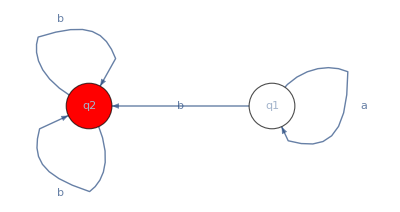

```mathematica
δ2=Association[
{"q1","a"}->"q1",{"q1","b"}->"q2",{"q2","b"}->"q2",{"q2","a"}->"q2"
];
ShowGraphDFA[δ2,{"q1", "q2"},"q1",{"q2"}]
```

```mathematica
FAstates2 = {"q1", "q2"};
initialStates2= "q1";
finalState2 = "q2";
nonFinalStates2 = {"q1"};
expressionVars2={q1,q2};
statesSeparation = {"q1" -> " q1 ","q2" -> " q2 "};
```

```mathematica
FAtoRe[δ2,FAstates2, initialStates2, finalState2, expressionVars2, statesSeparation, nonFinalStates2]
```

ab * + (a + b) *

## Ejemplo #3

```mathematica
δ3=Association[
{"q1","d"}->"q2",{"q1","e"}->"q3",{"q2","e"}->"q1",{"q3","d"}->"q1"
];
```

```mathematica
FAstates3 = {"q1", "q2", "q3"};
initialStates3= "q1";
finalState3 = "q1";
nonFinalStates3 = {"q2", "q3"};
expressionVars3={q1,q2, q3};
statesSeparation3 = {"q1" -> " q1 ","q2" -> " q2 ", "q3" -> " q3 "};
```

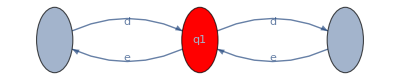

```mathematica
ShowGraphDFA[δ3,FAstates3,initialStates3,{finalState3}]
```

```mathematica
FAtoRe[δ3,FAstates3, initialStates3, finalState3, expressionVars3, statesSeparation3, nonFinalStates3]
```

(de + ed) *

## Pregunta 2 (30 pts)

### Problema

En clase hasta el momento hemos trabajado principalmente con autómatas de estado finito que procesan una cadena de caracteres y determinan si esta es válida o no.  Este es solamente un tipo de AEF que se conocen como Validadores, sin embargo hay otros tipos de autómatas que se pueden construir.

Por ejemplo se puede construir un autómata donde una transición puede generar no sólo un cambio de estado dependiendo de una entrada, sino puede cambiar variables de un sistema, o ejecutar acciones particulares en cada transición, también puede tener ciertos comportamientos mientras esté en un estado (actividades de estado).

Tomando en cuenta esto, ustedes se les ha encargado diseñar el control de movimiento de un robot que camina sobre una superficie irregular. El robot mueve dos apéndices (tipo patas) que están equipados con una colección de sensores:

Sensores de proximidad: el sensores retorna 1 si hay un obstáculo, y 0 si no los hay

Brújula: Controla el eje vertical de movimiento (yaw)

Clinómetro: detecta la inclinación cuando apoya uno de los apéndices

Construya un autómata que describa el movimiento (15 pts). Permita que cada transición represente información de entrada y  acciones de movimiento, y cada estado puede a su vez representar un conjunto de acciones (0 a n acciones). Sea detallado en la explicaciones de cada aspecto del autómata, y utilice una tabla de transiciones para explicar en detalle el significado de cada cambio (15 pts).

Este es un ejemplo hipotético, y en realidad no hay respuestas correctas, pero su solución representa una propuesta de control viable.

### Respuesta

Las siguientes son consideraciones a tener para poder entender el automata en cuestion: 
- 0 indica que no hay una lectura del sensor que indique una alteración en el terreno (inclinacion u obstaculo). Es decir, una respuesta de 1 en el sensor de proximidad significaría que hay un obstáculo y un 1 en la lectura del clinómetro indicaría que hay una inclinación. 
- La configuración del autómata está dada por 3 sensores y se describe como una secuencia entre 000 y 111 donde el primer digito indica si hay obstáculo, el segundo indica si hay inclinación y el tercero indica al autómata si debe girar o no (accion). 
- La configuración inicial es 000 y la misma indica que el autómata puede avanzar. 
Dadas las anteriores especificaciones se puede construir la siguiente tabla de transiciones:

Estado | Configuración | Obstáculo (O) | Acción | Inclinación (I) | Acción | Libre (L) | Acción
0 | 000 | 4 | Girar | 2 | Avanzar | 0 | Avanzar
1 | 001 | 1 | Girar | 0 | Avanzar | 0 | Avanzar
2 | 010 | 0 | Avanzar | 0 | Avanzar | 0 | Avanzar
3 | 011 | 7 | Parar | 2 | Avanzar | 2 | Avanzar
4 | 100 | 1 | Girar | 1 | Girar | 0 | Avanzar
5 | 101 | 5 | Girar | 3 | Avanzar | 0 | Avanzar
6 | 110 | 7 | Girar | 6 | Girar | 2 | Avanzar
7 | 111 | 7 | Parar | 3 | Girar | 2 | Avanzar

¿Cómo leer la tabla? Ejemplo: Para el estado 0 se introduce un obstáculo lo cuál hace que la configuración del autómata (estado) pase de 0 a 4, en cuyo caso la acción a tomar es GIRAR. Para el estado 0 se encuentra una inclinacion lo cual representa un cambio en la configuración del autómata y cambie de estado 0 a 2 sin ocasionar un problema para nuestro robot, permitiendole avanzar. Para el estado 0, si un espacio libre es presentado a nuestro robot ocasiona que el mismo ejecute la accion de avanzar. 

Tambien se deben tomar otras consideraciones para interpretar la tabla de esta manera: 
Estado: es una llave asignada para interpretar mas facilmente la configuracion del automata. Por ejemplo el estado 0 esta relacionado a la configuracion 000. 
Configuracion: Es una tripleta con informacion de los 2 sensores (proximidad, clinometro) y el controlador del eje vertical (yaw). 
Obstaculo, Inclinacion, Libre: Estas columnas indican que si uno de estos es presentado ante la configuracion evaluada en cada fila entonces produce un estado resultante. Por ejemplo, al estado 0 (configuracion 000) se le introduce un obstaculo entonces el resultado es el estado 4 (configuracion 100). 
Accion: Esta columna esta relacionada a que accion puede hacer el automata y esta relacionada a la configuracion del mismo. Por ejemplo, el estado 1 (configuracion 001) indica que el robot debe girar.

```mathematica
ShowGraph[δ_,states_List,q0_,q_List]:=Graph[
MapThread[DirectedEdge,{First/@Keys[δ],Values[δ]}],
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
EdgeWeight->Last/@Keys[δ],
EdgeLabels->"EdgeWeight",
VertexStyle->Join[{0->White},Map[(#->Red)&,q]]
]
```

```mathematica
DeltaHat[δ_,q0_,string_]:=FoldList[δ[{#1,#2}]&,q0,Characters[string]]
```

```mathematica
δ=Association[
{0,"O"}->4,
{0, "I"}->2,
{0, "L"}->0,
{1, "O"}->1,
{1, "I"}->0,
{1, "L"}->0, 
{2, "O"}->0, 
{2, "I"}->0,
{2, "L"}->0,
{3, "O"}->7,
{3, "I"} ->2,
{3, "L"}->2,
{4, "O"}->1,
{4, "I"}->1,
{4, "L"}->0,
{5, "O"}->5,
{5, "I"}->3,
{5, "L"}->0, 
{6, "O"}->7,
{6, "I"}->6,
{6, "L"}->2,
{7, "O"}->7,
{7,"I"}->3,
{7, "L"}->2
];
```

```mathematica
ShowGraph[δ,{8},0,{}];
```

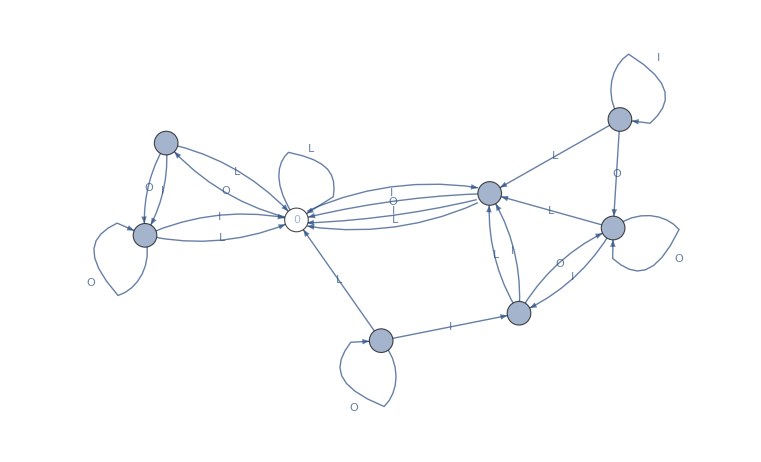

A continuacion, algunas pruebas.

```mathematica
DeltaHat[δ,0,"OILOI"]
```

{0,4,1,0,4,1}

```mathematica
DeltaHat[δ,0,"OOOOOOO"]
```

```mathematica
{0,4,1,1,1,1,1,1}
```

```mathematica
DeltaHat[δ,0,"OILOOOLLLILLIOLLIILLLO"]
```

{0,4,1,0,4,1,1,0,0,0,2,0,0,2,0,0,0,2,0,0,0,0,4}

## Pregunta 3 (10 pts)

### Problema

Considere la expresión regular (00+11)22*0, 
a) Construya un AEF  equivalente (5 pts)
b) Construya el AEF determinístico equivalente (5 pts)

Para efectos de entrega, entregar el procedimiento paso a paso que NO sean manuscritos, pero si pueden ser imágenes construidas en alguna otra aplicación, insertadas en este Notebook.

### Respuesta

AEF equivalente

Primero construimos las expresiones de los caracteres de la expresion

-Graphics-

Luego creamos 00

-Graphics-

Luego creamos 11

-Graphics-

Luego creamos  (00+11)

-Graphics-

Luego creamos 22*0

-Graphics-

Finalmente unimos todo (00+11)22*0

-Graphics-

AEF Deterministico